# QED calculation: Peskin Sec. 5

## e^+e^-→μ^+μ^- (QED): Peskin P.131-136

-Graphics-

### Initialization

You should choose English to avoid unnecessary confusions.

```mathematica
Exit[];
```

```mathematica
$Language="English";
```

```mathematica
<<FeynArts`
<<FormCalc`
```

FeynArts 3.10 (12 Mar 2018)

by Hagen Eck, Sepp Kueblbeck, and Thomas Hahn

FormCalc 9.6 (16 Apr 2018)

by Thomas Hahn

### Create Topology

TopologyList[Topology[1][Propagator[Incoming][Vertex[1][1],Vertex[4][5]],Propagator[Incoming][Vertex[1][2],Vertex[4][5]],Propagator[Outgoing][Vertex[1][3],Vertex[4][5]],Propagator[Outgoing][Vertex[1][4],Vertex[4][5]]],Topology[1][Propagator[Incoming][Vertex[1][1],Vertex[3][5]],Propagator[Incoming][Vertex[1][2],Vertex[3][5]],Propagator[Outgoing][Vertex[1][3],Vertex[3][6]],Propagator[Outgoing][Vertex[1][4],Vertex[3][6]],Propagator[Internal][Vertex[3][5],Vertex[3][6]]],Topology[1][Propagator[Incoming][Vertex[1][1],Vertex[3][5]],Propagator[Incoming][Vertex[1][2],Vertex[3][6]],Propagator[Outgoing][Vertex[1][3],Vertex[3][5]],Propagator[Outgoing][Vertex[1][4],Vertex[3][6]],Propagator[Internal][Vertex[3][5],Vertex[3][6]]],Topology[1][Propagator[Incoming][Vertex[1][1],Vertex[3][5]],Propagator[Incoming][Vertex[1][2],Vertex[3][6]],Propagator[Outgoing][Vertex[1][3],Vertex[3][6]],Propagator[Outgoing][Vertex[1][4],Vertex[3][5]],Propagator[Internal][Vertex[3][5],Vertex[3][6]]]]

> Top. 1 aebe/cede/0.m, 1 diagram

> Top. 2 aebe/cfdf/ef.m, 1 diagram

> Top. 3 aebf/cedf/ef.m, 1 diagram

> Top. 4 aebf/cfde/ef.m, 1 diagram



FeynArtsGraphics[2→2][([T1] | [T2] | [T3]
[T4] | Null | Null
Null | Null | Null)]

```mathematica
topologies=CreateTopologies[0,2->2]
Paint[topologies]
```

### Insert Particles

FeynArts Manual Appendix B has a list of the particles in the (default) SM model.

```mathematica
diagrams=InsertFields[topologies,{F[2,{1}],-F[2,{1}]}->{F[2,{2}],-F[2,{2}]},InsertionLevel->{Classes}]
```

loading generic model file /Users/misho/.ghq/github.com/HEPcodes/FeynArts/Models/Lorentz.gen

> $GenericMixing is OFF

generic model {Lorentz} initialized

loading classes model file /Users/misho/.ghq/github.com/HEPcodes/FeynArts/Models/SM.mod

$CKM=False

> 46 particles (incl. antiparticles) in 16 classes

> $CounterTerms are ON

> 88 vertices

> 115 counterterms of order 1

> 6 counterterms of order 2

classes model {SM} initialized

inserting at level(s) {Classes}

> Top. 1: 0 Classes insertions

> Top. 2: 4 Classes insertions

> Top. 3: 0 Classes insertions

> Top. 4: 0 Classes insertions

in total: 4 Classes insertions

TopologyList[Process→{F[2,{1}],-F[2,{1}]}→{F[2,{2}],-F[2,{2}]},Model→{SM},GenericModel→{Lorentz},InsertionLevel→{Classes},ExcludeParticles→{},ExcludeFieldPoints→{},LastSelections→{}][Topology[1][Propagator[Incoming][Vertex[1][1],Vertex[3][5],Field[1]],Propagator[Incoming][Vertex[1][2],Vertex[3][5],Field[2]],Propagator[Outgoing][Vertex[1][3],Vertex[3][6],Field[3]],Propagator[Outgoing][Vertex[1][4],Vertex[3][6],Field[4]],Propagator[Internal][Vertex[3][5],Vertex[3][6],Field[5]]]→Insertions[Generic][FeynmanGraph[1,Generic==1][Field[1]→F[2,{1}],Field[2]→-F[2,{1}],Field[3]→-F[2,{2}],Field[4]→F[2,{2}],Field[5]→S]→Insertions[Classes][FeynmanGraph[1,Classes==1][Field[1]→F[2,{1}],Field[2]→-F[2,{1}],Field[3]→-F[2,{2}],Field[4]→F[2,{2}],Field[5]→S[1]],FeynmanGraph[1,Classes==2][Field[1]→F[2,{1}],Field[2]→-F[2,{1}],Field[3]→-F[2,{2}],Field[4]→F[2,{2}],Field[5]→S[2]]],FeynmanGraph[1,Generic==2][Field[1]→F[2,{1}],Field[2]→-F[2,{1}],Field[3]→-F[2,{2}],Field[4]→F[2,{2}],Field[5]→V]→Insertions[Classes][FeynmanGraph[1,Classes==1][Field[1]→F[2,{1}],Field[2]→-F[2,{1}],Field[3]→-F[2,{2}],Field[4]→F[2,{2}],Field[5]→V[1]],FeynmanGraph[1,Classes==2][Field[1]→F[2,{1}],Field[2]→-F[2,{1}],Field[3]→-F[2,{2}],Field[4]→F[2,{2}],Field[5]→V[2]]]]]

> Top. 1 aebe/cfdf/ef.m, 4 diagrams

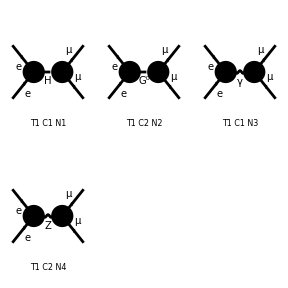

FeynArtsGraphics[{e,e}→{\mu,\mu}][([T1 C1 N1] | [T1 C2 N2] | [T1 C1 N3]
[T1 C2 N4] | Null | Null
Null | Null | Null)]

```mathematica
Paint[diagrams]
```

### Insert Particles (again...)

Excluding 0 Generic, 3 Classes, and 3 Particles fields

inserting at level(s) {Classes}

> Top. 1: 0 Classes insertions

> Top. 2: 1 Classes insertion

> Top. 3: 0 Classes insertions

> Top. 4: 0 Classes insertions

Restoring 0 Generic, 3 Classes, and 3 Particles fields

in total: 1 Classes insertion

> Top. 1 aebe/cfdf/ef.m, 1 diagram

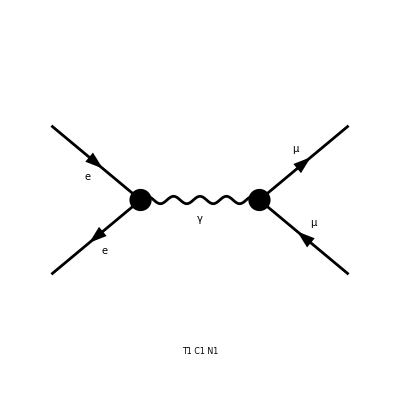

```mathematica
(* We concentrate on QED for simplicity. *)
diagrams=InsertFields[topologies,{F[2,{1}],-F[2,{1}]}->{F[2,{2}],-F[2,{2}]},InsertionLevel->{Classes},
	ExcludeParticles->{V[2],S[1],S[2]}];
Paint[diagrams];
```

### Pass the diagram to FormCalc

```mathematica
ClearProcess[];
amplitude=CalcFeynAmp[CreateFeynAmp[diagrams],FermionChains->VA];
matrix=SquaredME[amplitude]//.HelicityME[amplitude]
```

creating amplitudes at level(s) {Classes}

> Top. 1: 1 Classes amplitude

in total: 1 Classes amplitude

preparing FORM code in /Users/misho/fc-amp-1.frm

running FORM...

ok

> 1 helicity matrix elements

preparing FORM code in /Users/misho/fc-hel-1.frm

running FORM...

ok

{FF[F1] FFC[F1] (1/2 (T^2+2 (ME2^2+MM2^2+MM2 (S-T-U)+ME2 (2 MM2+S-T-U))+U^2)+Hel[1] ((Abb4-2 ME2 (Abb1+MM2 Pair5)) Hel[2]+2 Abb5 ME MM Hel[3])+(Abb17-2 MM2 (Abb9+ME2 Pair18)-1/2 (Abb21-2 (Abb11 ME2+(Abb10+2 Abb2 ME2) MM2)) Hel[1] Hel[2]) Hel[3] Hel[4]+2 ME MM (Abb7 Hel[2] Hel[3]+(Abb6 Hel[1]+Abb8 Hel[2]) Hel[4])),{FF[F1]→-4 Alfa π Den[S,0],FFC[F1]→-4 Alfa π Den[S,0]}}

```mathematica
(* Assumes unpolarized fermions *)
matrix = matrix//.Hel[_]->0
```

{1/2 (T^2+2 (ME2^2+MM2^2+MM2 (S-T-U)+ME2 (2 MM2+S-T-U))+U^2) FF[F1] FFC[F1],{FF[F1]→-4 Alfa π Den[S,0],FFC[F1]→-4 Alfa π Den[S,0]}}

-Graphics-

```mathematica
matrix//.Abbr[]//.Subexpr[]//.{Den[p2_,m2_]:>1/(p2-m2),Alfa->e^2/(4π),Alfa2->(e^2/(4π))^2,ME2->0}
```

{1/2 (T^2+2 (MM2^2+MM2 (S-T-U))+U^2) FF[(<v1|1,Lor[1]|u2>) (<u3|1,Lor[1]|v4>)] FFC[(<v1|1,Lor[1]|u2>) (<u3|1,Lor[1]|v4>)],{FF[(<v1|1,Lor[1]|u2>) (<u3|1,Lor[1]|v4>)]→-e^2/S,FFC[(<v1|1,Lor[1]|u2>) (<u3|1,Lor[1]|v4>)]→-e^2/S}}

```mathematica
%//.{S->4 EE^2,T->MM^2-2(EE^2-EE √(EE^2-MM^2)CosTheta),U->-S-T+2MM2}
```

{1/2 ((-2 (EE^2-CosTheta EE √(EE^2-MM2))+MM2)^2+(-4 EE^2+2 (EE^2-CosTheta EE √(EE^2-MM2))+MM2)^2+2 ((8 EE^2-2 MM2) MM2+MM2^2)) FF[(<v1|1,Lor[1]|u2>) (<u3|1,Lor[1]|v4>)] FFC[(<v1|1,Lor[1]|u2>) (<u3|1,Lor[1]|v4>)],{FF[(<v1|1,Lor[1]|u2>) (<u3|1,Lor[1]|v4>)]→-e^2/(4 EE^2),FFC[(<v1|1,Lor[1]|u2>) (<u3|1,Lor[1]|v4>)]→-e^2/(4 EE^2)}}

```mathematica
%[[1]]//.%[[2]]
```

(e^4 ((-2 (EE^2-CosTheta EE √(EE^2-MM2))+MM2)^2+(-4 EE^2+2 (EE^2-CosTheta EE √(EE^2-MM2))+MM2)^2+2 ((8 EE^2-2 MM2) MM2+MM2^2)))/(32 EE^4)

```mathematica
Collect[FullSimplify[%],{e,CosTheta}]
```

e^4 ((CosTheta^2 (EE^2-MM2))/(4 EE^2)+(EE^2+MM2)/(4 EE^2))

This is different from the result in Peskin’s book.
We should be very careful to use tools for automatic calculation.

### Doing again with patience.

```mathematica
ClearProcess[];
amplitude=CalcFeynAmp[CreateFeynAmp[diagrams],FermionChains->Weyl]
```

creating amplitudes at level(s) {Classes}

> Top. 1: 1 Classes amplitude

in total: 1 Classes amplitude

preparing FORM code in /Users/misho/fc-amp-1.frm

running FORM...

ok

Amp[{{F[2,{1}],k[1],ME,{-Charge,LeptonNumber}},{-F[2,{1}],k[2],ME,{Charge,-LeptonNumber}}}→{{F[2,{2}],k[3],MM,{-Charge,LeptonNumber}},{-F[2,{2}],k[4],MM,{Charge,-LeptonNumber}}}][-8 Alfa π Sub1 Den[S,0]]

Here we used “Weyl” as an option, which is the default according to the manual.
Because this process is vector-like (i.e. not chiral), we use “VA” as the FermionChains option.

```mathematica
ClearProcess[];
amplitude=CalcFeynAmp[CreateFeynAmp[diagrams],FermionChains->VA]
```

creating amplitudes at level(s) {Classes}

> Top. 1: 1 Classes amplitude

in total: 1 Classes amplitude

preparing FORM code in /Users/misho/fc-amp-1.frm

running FORM...

ok

Amp[{{F[2,{1}],k[1],ME,{-Charge,LeptonNumber}},{-F[2,{1}],k[2],ME,{Charge,-LeptonNumber}}}→{{F[2,{2}],k[3],MM,{-Charge,LeptonNumber}},{-F[2,{2}],k[4],MM,{Charge,-LeptonNumber}}}][-4 Alfa π Den[S,0] Mat[F1]]

Here you see the incoming and outgoing particles with, e.g., momentum “k[1]”, mass “ME”, etc.
The “amplitude” is the last object, which is

```mathematica
amplitude[[1]]
```

-4 Alfa π Den[S,0] Mat[F1]

with some abbreviations. You can expand the abbreviations by

```mathematica
amplitude[[1]] //. Join[Abbr[],Subexpr[]]
```

-4 Alfa π Den[S,0] Mat[(<v1|1,Lor[1]|u2>) (<u3|1,Lor[1]|v4>)]

Here,  “Abbr[]” and “Subexpr[]” give the abbreviations used in this calculation.

```mathematica
Abbr[]
```

{F1→(<v1|1,Lor[1]|u2>) (<u3|1,Lor[1]|v4>)}

```mathematica
Subexpr[]
```

{Sub1→Removed[F1] Removed[F5]+Removed[F2] Removed[F6]+Removed[F3] Removed[F7]+Removed[F4] Removed[F8]}

Then we square the matrix element.

```mathematica
squared = SquaredME[amplitude]
```

{FF[F1] FFC[F1] Mat[F1,F1],{FF[F1]→-4 Alfa π Den[S,0],FFC[F1]→-4 Alfa π Den[S,0]}}

In FormCalc v9.6 (and later), SquaredME returns a list of {squared, squaredRules} to improve calculation speed.
Theoretically we should apply these rules as late as possible, but in this first lecture we apply them right now so that you are not confused by the compressed notation.

```mathematica
squaredWithRules=SquaredME[amplitude]
squared=squaredWithRules[[1]]//.squaredWithRules[[2]]
```

{FF[F1] FFC[F1] Mat[F1,F1],{FF[F1]→-4 Alfa π Den[S,0],FFC[F1]→-4 Alfa π Den[S,0]}}

16 Alfa2 π^2 Den[S,0]^2 Mat[F1,F1]

Then we apply HelicityME.

```mathematica
squared//.HelicityME[amplitude]
```

> 1 helicity matrix elements

preparing FORM code in /Users/misho/fc-hel-1.frm

running FORM...

ok

16 Alfa2 π^2 Den[S,0]^2 (1/2 (T^2+2 (ME2^2+MM2^2+MM2 (S-T-U)+ME2 (2 MM2+S-T-U))+U^2)+Hel[1] ((Abb4-2 ME2 (Abb1+MM2 Pair5)) Hel[2]+2 Abb5 ME MM Hel[3])+(Abb13-2 MM2 (Abb8+ME2 Pair13)-1/2 (Abb21-2 (Abb6 ME2+(Abb9+2 Abb2 ME2) MM2)) Hel[1] Hel[2]) Hel[3] Hel[4]+2 ME MM (Abb10 Hel[2] Hel[3]+(Abb7 Hel[1]+Abb11 Hel[2]) Hel[4]))

Hmm... anyway we want to remove the helicity....

```mathematica
squared//.HelicityME[amplitude]//.{Hel[1]->0,Hel[2]->0,Hel[3]->0,Hel[4]->0}
```

> 1 helicity matrix elements

preparing FORM code in /Users/misho/fc-hel-1.frm

running FORM...

ok

8 Alfa2 π^2 (T^2+2 (ME2^2+MM2^2+MM2 (S-T-U)+ME2 (2 MM2+S-T-U))+U^2) Den[S,0]^2

This is actually THE AVERAGE over the helicity! Because we want to average for the incoming states, while to sum over the outgoing, we have to multiply by four.

```mathematica
result=4*squared//.HelicityME[amplitude]//.{Hel[1]->0,Hel[2]->0,Hel[3]->0,Hel[4]->0}
result//.{Den[p2_,m2_]:>1/(p2-m2),Alfa->e^2/(4π),Alfa2->(e^2/(4π))^2,ME2->0}//.{S->4 EE^2,T->MM^2-2(EE^2-EE √(EE^2-MM^2)CosTheta),U->-T-S+2MM2}
```

> 1 helicity matrix elements

preparing FORM code in /Users/misho/fc-hel-1.frm

running FORM...

ok

32 Alfa2 π^2 (T^2+2 (ME2^2+MM2^2+MM2 (S-T-U)+ME2 (2 MM2+S-T-U))+U^2) Den[S,0]^2

(e^4 ((-2 (EE^2-CosTheta EE √(EE^2-MM2))+MM2)^2+(-4 EE^2+2 (EE^2-CosTheta EE √(EE^2-MM2))+MM2)^2+2 ((8 EE^2-2 MM2) MM2+MM2^2)))/(8 EE^4)

```mathematica
Collect[FullSimplify[%],{e,CosTheta},Expand]
```

e^4 (1+MM2/EE^2+CosTheta^2 (1-MM2/EE^2))

-Graphics-

Perfect.